```mathematica
SetOptions[EvaluationNotebook[],AutoGeneratedPackage->"AnSEL.m"]
```

# AnSEL - Analysis and Simplification of Equations with Loops

## Exports

```mathematica
SetLoopMomentumName::usage=""

RouteIndices::usage=""
RouteIndices[expr_FEq]/;Head[$GlobalSetup]=!=Symbol:=RouteIndices[$GlobalSetup,expr];
```

## Global variables

```mathematica
ModuleLoaded::dependency="The module `1` requires `2`, which has not been loaded.";

If[ModuleLoaded[FunKit]=!=True,
Message[ModuleLoaded::dependency,"FEDeriK","FunKit"];
Abort[];
];

If[ModuleLoaded[FEDeriK]=!=True,
Message[ModuleLoaded::dependency,"FEDeriK","FunKit"];
Abort[];
];

ModuleLoaded[AnSEL]=True;

$loopMomentumName="l";
Unprotect@@Table[$loopMomentumName<>ToString[idx],{idx,1,50}];
ClearAll@@Table[$loopMomentumName<>ToString[idx],{idx,1,50}];
Protect@@Table[$loopMomentumName<>ToString[idx],{idx,1,50}];
Unprotect[$availableLoopMomenta];
$availableLoopMomenta=Table[Symbol[$loopMomentumName<>ToString[idx]],{idx,1,50}];
Protect[$availableLoopMomenta];
```

```mathematica
SetLoopMomentumName[name_String]:=Module[{},
Unprotect@@Table[$loopMomentumName<>ToString[idx],{idx,1,50}];
$loopMomentumName=name;
ClearAll@@Table[$loopMomentumName<>ToString[idx],{idx,1,50}];
Protect@@Table[$loopMomentumName<>ToString[idx],{idx,1,50}];
Unprotect[$availableLoopMomenta];
$availableLoopMomenta=Table[$loopMomentumName<>ToString[idx],{idx,1,50}];
Protect[$availableLoopMomenta];
];
```

```mathematica
$FunKitDirectory=SelectFirst[Join[{FileNameJoin[{$UserBaseDirectory,"Applications","FunKit"}],FileNameJoin[{$BaseDirectory,"Applications","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","Applications","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","Packages","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","ExtraPackages","FunKit"}]},Select[$Path,StringContainsQ[#,"FunKit"]&]],DirectoryQ[#]&]<>"/";
```

## Index routing

```mathematica
(*A convenience function to quickly obtain the index structure of a given field.*)
FieldSetupIndices[setup_,field_]:=Module[{},
List@@SelectFirst[
Flatten@Values[setup["FieldSpace"]],
Head[#]===field&
]
];
```

```mathematica
RouteIndices::undeterminedFields="Cannot route indices in expressions with undetermined fields.";
RouteIndices::momentaFailed="Cannot route momenta in the given expression.";

RouteIndices[setup_,expr_FTerm]:=Module[
{openIndices,closedIndices,objects,
ret=ReduceFTerm[setup,ReduceIndices[setup,expr]],doFields,idx,a,
indPos,assocField,subObj,subMom,subExtMom,
indStruct,externalIndices,externalMomenta,
f,momRepl,A1111111,AA111111,i,mom,loopMomenta
},

(*We first get all closed, open indices and all indexed objects.*)
doFields=Thread[(#[a__]&/@GetAllFields[setup])->(Field[{#},{a}]&/@GetAllFields[setup])];
openIndices=Sort@GetOpenSuperIndices[setup,ret];
closedIndices=GetClosedSuperIndices[setup,ret];
objects=ExtractObjectsWithIndex[setup,ret]//.doFields;

(*If there are any undetermined fields, we cannot route indices.*)
If[MemberQ[objects[[All,1]],AnyField,{1,4}],Message[RouteIndices::undeterminedFields];Abort[]];

(*As a first step, we insert the correct index structures into all superindices and define momentum variables at every single vertex.
We loop over all closed indices.*)
Do[
(*The indexed object we currently modify. There are always two and we simply grab the first.*)
subObj=Select[objects,MemberQ[#,closedIndices[[idx]],Infinity]&][[1]];
(*The position of the current index inside the subObj*)
indPos=FirstPosition[subObj[[2]],closedIndices[[idx]]][[1]];
(*See what kind of field is associated with the index*)
assocField=subObj[[1,indPos]];
(*Grab the index structure of this field from the setup and assign a new momentum variable*)
indStruct=Map[If[MatchQ[#,_Symbol],Unique[SymbolName[#]],#]&,FieldSetupIndices[setup,assocField],{1,3}];
indStruct[[1]]=loopMomentum[indStruct[[1]]];

(*replace all occurences of the superindex with the fitting index structure. 
We want to keep the index sign in the momenta, but remove it from the group indices*)
ret=ret/.closedIndices[[idx]]->indStruct;
ret=ret/.(-indStruct[[2]])->indStruct[[2]];
objects=objects/.closedIndices[[idx]]->indStruct;
objects=objects/.(-indStruct[[2]])->indStruct[[2]];

,{idx,1,Length[closedIndices]}];

(*Next, we treat the external superindices. We assign to each an open group structure and a new momentum p1,p2,... 
Momentum conservation is already enforced here, i.e. ∑_i Subscript[p, i]=0 and we choose Subscript[p, n]=-∑_(i<n) Subscript[p, i] for the last momentum Subscript[p, n].*)
externalIndices=Table[{},{idx,1,Length[openIndices]}];
Do[
(*see above*)
subObj=Select[objects,MemberQ[#,openIndices[[idx]],Infinity]&][[1]];
indPos=FirstPosition[subObj[[2]],openIndices[[idx]]][[1]];
assocField=subObj[[1,indPos]];
indStruct=Map[If[MatchQ[#,_Symbol],Symbol[SymbolName[#]<>ToString[idx]],#]&,FieldSetupIndices[setup,assocField],{1,3}];

(*Subscript[p, n]=-∑_(i<n) Subscript[p, i]*)
If[idx===Length[openIndices],indStruct[[1]]=-Total[Values[externalIndices][[;;idx-1,1]]]];

ret=ret/.openIndices[[idx]]->indStruct;
ret=ret/.(-indStruct)->indStruct;
objects=objects/.openIndices[[idx]]->indStruct;
objects=objects/.(-indStruct)->indStruct;

(*This is information for the user, which we will return.*)
externalIndices[[idx]]=openIndices[[idx]]->indStruct;

,{idx,1,Length[openIndices]}];

(*extract a list of all new external momenta*)
externalMomenta=Values[externalIndices][[All,1]];

(*Now, we do the momentum routing.*)
Do[
subObj=objects[[idx]];
subMom=subObj[[2,All,1]];
(*See if the object has any external (sub-)momenta*)
subExtMom=Select[subMom,(ContainsAny[externalMomenta,makePosIdx/@Flatten[{#/.Plus[a_,b__]:>List[a,b]}]])&];

(*if momentum conservation is already fulfilled, do nothing*)
If[Total@subMom===0,Continue[]];

(*Case 1: we have no external momentum anywhere in the legs of the current object*)
If[Length[subExtMom]===0,
(*for safety, we try to route our momenta through fermions. At 1-loop this is irrelevant, at n-loop it is not.*)
f=FirstPosition[IsFermion[setup,#]&/@subObj[[1]],True][[1]];
If[f==="NotFound",f=1];

mom=Select[Flatten[{subObj[[2,f,1]]/.Plus[a_,b__]:>List[a,b]}],(MatchQ[#,loopMomentum[_]]||MatchQ[-#,loopMomentum[_]])&][[1]];
momRepl=If[isNeg[mom],
-mom->-mom+Total[subObj[[2,All,1]]],
mom->mom-Total[subObj[[2,All,1]]]
];

objects=objects/.momRepl;
ret=ret/.momRepl;

Continue[];
];

(*Case 2: we have at least one momentum without an external one*)
If[Length[subExtMom]<Length[subMom],
(*for safety, we try to route our momenta through fermions.*)
f=FirstPosition[
Table[
(IsFermion[setup,subObj[[1,i]]]&&ContainsNone[externalMomenta,makePosIdx/@Flatten[{subObj[[2,i,1]]/.Plus[a_,b__]:>List[a,b]}]])
,{i,1,Length[subObj[[1]]]}]
,True][[1]];
(*If no fermions are present, simply grab the index which does not contain external momenta.*)
If[f==="NotFound",
f=FirstPosition[
Table[(ContainsNone[externalMomenta,makePosIdx/@Flatten[{subObj[[2,i,1]]/.Plus[a_,b__]:>List[a,b]}]])
,{i,1,Length[subObj[[1]]]}]
,True][[1]];
];

mom=Select[Flatten[{subObj[[2,f,1]]/.Plus[a_,b__]:>List[a,b]}],(MatchQ[#,loopMomentum[_]]||MatchQ[-#,loopMomentum[_]])&][[1]];
momRepl=If[isNeg[mom],
-mom->-mom+Total[subObj[[2,All,1]]],
mom->mom-Total[subObj[[2,All,1]]]
];

objects=objects/.momRepl;
ret=ret/.momRepl;

Continue[];
];

Abort[];
,{idx,1,Length[objects]}];

(*Sanity check to see that we did not make an error*)
Do[
subObj=objects[[idx]];
If[Total[subObj[[2,All,1]]]=!=0,Message[RouteIndices::momentaFailed];Abort[]];
,{idx,1,Length[objects]}];

(*replace the loopMomenta[...] by l1, l2, ...*)
loopMomenta=Cases[objects[[All,2,1]],loopMomentum[_],Infinity]//DeleteDuplicates;
ret=ret/.Thread[loopMomenta->Table[Symbol[$loopMomentumName<>ToString[idx]],{idx,1,Length[loopMomenta]}]];
loopMomenta=loopMomenta/.Thread[loopMomenta->Table[Symbol[$loopMomentumName<>ToString[idx]],{idx,1,Length[loopMomenta]}]];

Return[<|
"result"->FEq[ret],
"externalIndices"->externalIndices,
"loopMomenta"->loopMomenta
|>];
];

RouteIndices[setup_,expr_FEq]:=Module[{results,ret,idx,subidx},
results=RouteIndices[setup,#]&/@(List@@expr);

(*All terms have the same loop momenta and external legs*)
If[Equal@@Map[#["loopMomenta"]&,results]&&
Equal@@Map[#["externalIndices"]&,results],
Return[<|
"result"->FEq@@Map[#["result"]&,results],
"externalIndices"->results[[1]]["externalIndices"],
"loopMomenta"->results[[1]]["loopMomenta"]
|>]
];

(*All terms have the same external legs, but different loop orders*)
If[Equal@@Map[#["externalIndices"]&,results],
ret={results[[1]]};
Do[
For[subidx=1,subidx<=Length[ret]+1,subidx++,
If[subidx===Length[ret]+1,
AppendTo[ret,results[[idx]]];
Break[];
];
If[ret[[subidx]]["loopMomenta"]===results[[idx]]["loopMomenta"],
ret[[subidx,Key["result"]]]=FEq[ret[[subidx,Key["result"]]],results[[idx]]["result"]];
Break[];
];
];
,{idx,2,Length[results]}];
Return[SortBy[ret,Length[#["loopMomenta"]]&]]
];

(*All terms are different*)
Return[results];
];
```

## Identification of expressions

```mathematica
FTerm[λ[f]Propagator[{A,A},{x,y}]]
```

FTerm[Propagator[{A,A},{x,y}] λ[f]]

```mathematica
ClearAll[followLoop,GetLoops,i];
followLoop[setup_,term_FTerm,openIndices_,closedIndices_,allObj_,start_,startIdx_,oldmemory_:{}]:=Module[
{memory=oldmemory,curPos=start,curIdx=startIdx,curIndices,nextIdx,continue=True},
i=1;
While[i<9,
curIndices=makePosIdx/@curPos[[2]];
nextIdx=Select[curIndices,(#=!=curIdx&&FreeQ[openIndices,#])&];
(*Print["cur is ",curIdx," and ",nextIdx];*)
If[Length[memory]>0&&curPos===memory[[1]],Print[oi];Break[]];
If[Length[nextIdx]===1||Length[memory]===0,
AppendTo[memory,curPos];
curPos=Select[allObj,(MemberQ[#[[2]],nextIdx[[1]],{1,4}]&&#=!=curPos)&][[1]];
curIdx=nextIdx[[1]];
(*Print[curPos];*)
];
i++;
];
Return[memory];
];

GetLoops[setup_,expr_FTerm]:=Module[
{doFields,term,
openIndices,closedIndices,allObj,firsts,i},
doFields=Thread[(#[a__]&/@GetAllFields[setup])->(Field[{#},{a}]&/@GetAllFields[setup])];
term=expr/.doFields;
openIndices=GetOpenSuperIndices[setup,expr];
closedIndices=GetClosedSuperIndices[setup,expr];
allObj=ExtractObjectsWithIndex[setup,expr]/.doFields;

firsts=Table[
Select[allObj,MemberQ[#[[2]],openIndices[[i]],Infinity]&][[1]]
,{i,1,Length[openIndices]}];
Table[
followLoop[setup,expr,openIndices,closedIndices,allObj,firsts[[i]],openIndices[[i]]]
,{i,1,Length[firsts]}]

];
TakeDerivatives[WetterichEquation,{A[i1]}]//Truncate;
GetLoops[Setup,%[[1]]]
```

oi

{{GammaN[{c,cb,A},{-ic$5225,-id$5226,-i1}],Propagator[{cb,c},{a$5223,ic$5225}],Rdot[{c,cb},{-b$5224,-a$5223}],Propagator[{cb,c},{id$5226,b$5224}]}}

```mathematica
StartPoints[setup_,t1_FTerm,t2_FTerm]:=Module[
{obj1,obj2,count,
desired,sList,
match1,match2},
obj1=Sort@Select[ExtractObjectsWithIndex[setup,t1],MemberQ[$indexedObjects,Head@#]&];
obj2=Sort@Select[ExtractObjectsWithIndex[setup,t2],MemberQ[$indexedObjects,Head@#]&];
If[Map[Head[#][#[[1]]]&,obj1]=!=Map[Head[#][#[[1]]]&,obj2],Return[{False,Null}]];
sList=Map[Head[#][#[[1]]]&,obj1];
count=Counts[sList];
desired=Keys[count][[PositionSmallest[Values[count]][[-1]]]];
match1=Select[obj1,(Head[#][#[[1]]]===desired)&][[1]];
match2=Select[obj1,(Head[#][#[[1]]]===desired)&][[1]];
Return[{True,{obj1[[#]],obj2[[#]]}&@PositionSmallest[count]}]
]

test1=TakeDerivatives[WetterichEquation,{A[i1]}]//Truncate;
test2=TakeDerivatives[WetterichEquation,{A[i1]}]//Truncate;
StartPoints[Setup,test1[[1]],test2[[1]]**FTerm[Propagator[{A,A},{x,y}]]]
StartPoints[Setup,test1[[1]],test2[[1]]]
```

{False,Null}

Rdot[{c,cb}]

{True,{{GammaN[{c,cb,A},{-ic$839,-id$840,-i1}],Propagator[{cb,c},{id$840,b$838}]},{GammaN[{c,cb,A},{-ic$857,-id$858,-i1}],Propagator[{cb,c},{id$858,b$856}]}}}

```mathematica
WetterichEquation//FPrint
```

-Graphics-

```mathematica
MakeDSE[c[x]]
```

FEq[FTerm[S[{c,cb},{-x,-i99}],cb[i99]],FTerm[S[{c,cb,A},{-x,-i110,-i111}],A[i111] cb[i110]],FTerm[S[{c,cb,A},{-x,-i50,-i51}],Propagator[{cb,AnyField},{i50,i$52}],γ[{AnyField,A},{-i$52,i51}]]]

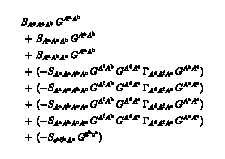

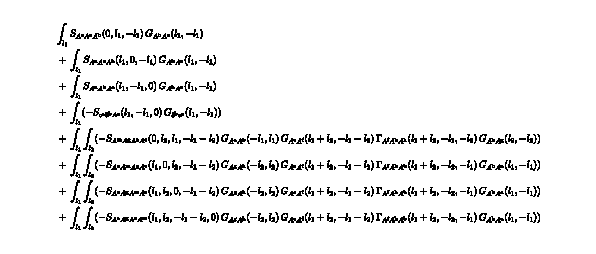

```mathematica
(MakeDSE[A[x]]//.{A[_]:>0,c[_]:>0,cb[_]:>0})//Truncate;
%//FPrint
RouteIndices[Setup,%%];
%//FPrint
```

# Testing

```mathematica
Get["FunKit`"]
```

Loading modules...

...TensorBases loaded

...FEDeriK loaded

...AnSEL loaded

...DiANE loaded

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 1.0
Year: 2025
For more information, call FunKitInfo[].

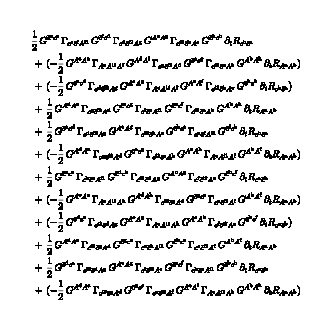

```mathematica
fields= <|
"cField"-> {
A[p,{v, c}]
},
"Grassmann"->{
{cb[p,{c}],c[p,{c}]}
}
|>;
truncation=<|
GammaN->{
{A,A},{A,A,A},{A,A,A,A},
{A,cb,c}
},
Propagator->{
{A,A},{cb,c}
},
Rdot->{
{A,A},{cb,c}
},
S->{
{A,A},{A,A,A},{A,A,A,A},
{cb,c},{cb,c,A}
}
|>;
SetTexStyles[cb->"\\bar{c}"];
masterEquation={
{1/2 A[x]VBasis[{A,A},{-x,-y}]A[y]},
{-cb[x]VBasis[{cb,c},{-x,-y}],c[y]}
};
Setup:=<|
"MasterEquation"->masterEquation,
"FieldSpace"->fields,
"Truncation"->truncation
|>;
SetGlobalSetup[Setup];
DerivativeListAcbc={ A[i1],cb[i2],c[i3]};
TakeDerivatives[Setup,WetterichEquation,DerivativeListAcbc];
%//Truncate//FPrint
```